# TMD Evolution author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/DY/mathematica

## Constants :

```mathematica
Λ = 0.2;
CF = 4/3;
Nf = 3;
beta0 = (33 - 2 Nf)/(12 π);
Q0 = 1.3;  (* Starting scale for evolution. *)
(*Q0 = 0.45; (* Starting scale for evolution fro models. *) *)
MZ = 91.19;

bmax = 1.;


bstar[bt_] := bt/ Sqrt[1 + bt^2 / bmax^2]; (* b* *)


C1 = 2 Exp[-N[EulerGamma]];   
mub[bt_] := C1 / bstar[bt]; (* mub *)
```

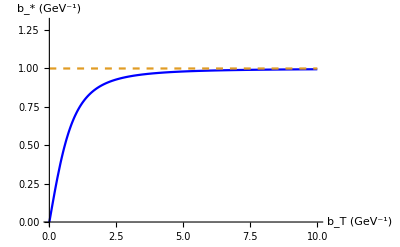

```mathematica
Plot[{bstar[bt],bmax},{bt,0,10},AxesLabel->{"b_T (GeV^-1)","b_* (GeV^-1)"},PlotRange->{0,1.3},PlotStyle->{Blue,Dashed}]
```

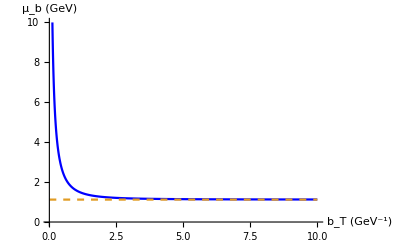

```mathematica
Plot[{mub[bt],C1/bmax},{bt,0,10},AxesLabel->{"b_T (GeV^-1)","μ_b (GeV)"},PlotRange->{0,10},PlotStyle->{Blue,Dashed}]
```

## QCD strong coupling, alpha s

#### Let us start by constructing a 2 loop solution compatible with CTEQ parametrization

```mathematica
Lambda[Q_]:=Piecewise[{{0.372205,Q≤1.3},{0.325603,1.3≤Q<4.5},{0.2259965,4.5≤Q}}];
NF[Q_]:=Piecewise[{{3,Q≤1.3},{4,1.3≤Q<4.5},{5,4.5≤Q}}];
β[Q_]:=11-2/3 NF[Q];
β1[Q_]:=51-19/3 NF[Q];

AlphaS[Q_]:=
(4π)/(β[Q]Log[Q^2/Lambda[Q]^2])(1-(2β1[Q])/β[Q]^2 Log[Log[Q^2/Lambda[Q]^2]]/Log[Q^2/Lambda[Q]^2])
```

```mathematica
AlphaS[MZ]
```

0.117981

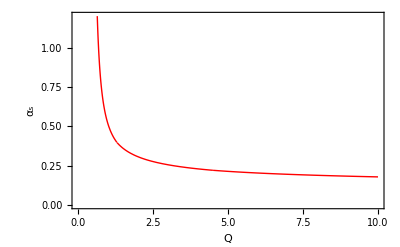

```mathematica
Plot[AlphaS[Q],{Q,0.5,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,1.2}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","α_s"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

#### Let us also use a simple solution that we will “tune” to the 2 loop one in the region of interest Q in 1.3 (our initial scale) to 10

```mathematica
as[Q_]:= 1/(beta0 Log[Q^2/Λ^2])
```

Clearly at very high Q solutions will diverge from each other, i.e. at MZ

```mathematica
as[MZ]
AlphaS[MZ]
```

0.114029

0.117981

```mathematica
as[0.45]
```

0.860902

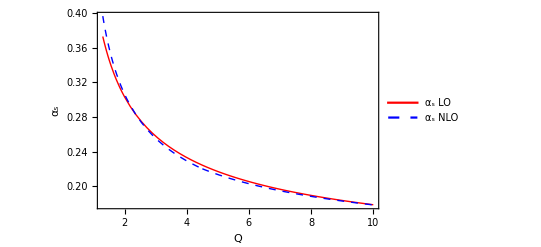

```mathematica
Plot[{as[Q],AlphaS[Q]},{Q,1.3,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","α_s"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"α_s LO","α_s NLO"},{0.7,0.7}]]
```

## Perturbative evolution

One loop result using one loop alpha_s

```mathematica
Spert[Q_]:=-(2 CF)/(π beta0)(Log[Q/Q0]-Log[Q/Λ]Log[Log[Q/Λ]/Log[Q0/Λ]]+3/4 Log[Log[Q/Λ]/Log[Q0/Λ]])
```

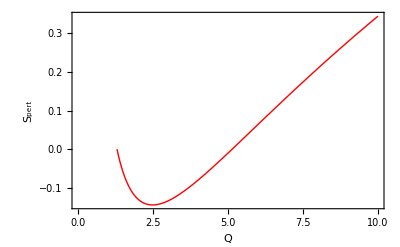

```mathematica
Plot[Spert[Q],{Q,Q0,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","S_pert"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

Notice Sperp becomes negative.

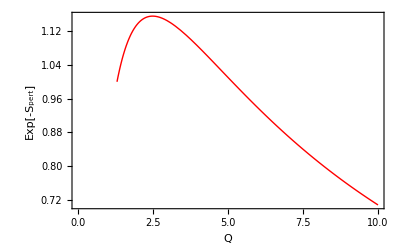

```mathematica
Plot[Exp[-Spert[Q]],{Q,Q0,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","Exp[-S_pert]"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

It results in an enhancement instead of suppression for some region in Q.

## Collins-Soper evolution kernel K̃ , it gives the Q-dependent change in the distribution, a very characteristic effect of the gluon emissions

One loop solution:

```mathematica
KtildePert[b_,Q_]:= -as[Q]/π(Log[(b^2 Q^2)/4]+ 2 N[EulerGamma])
```

```mathematica
Plot3D[KtildePert[b,Q],{b,0,1},{Q,Q0,10}]
```

-Graphics3D-

It looks like this at the initial scale Q0:

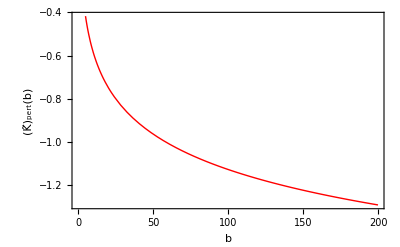

```mathematica
Plot[KtildePert[b,Q0],{b,0,200},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b","(K̃)_pert(b)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

At large values of b, K̃, tends to a negative constant

K̃ from Collins, Rogers PRD 91,(2015)
 
 gK from Eq.(79)

```mathematica
g0 = (as[C1/bmax] CF)/π ; (* it is the lower limit, actually, can be bigger, see discussion after Eq. (83) from PRD 91*)
(* g0 = 0.4; *)
gK[b_] := g0 ( 1-Exp[-(as[mub[b]] CF b^2)/(π g0 bmax^2) ]); (*model for non perturbative dynamics in CS kernel from PRD 91*)
gKYuan[b_] := 0.84 Log[b/bstar[b]];  (* this one is from my paper with Kang and Yan *)
```

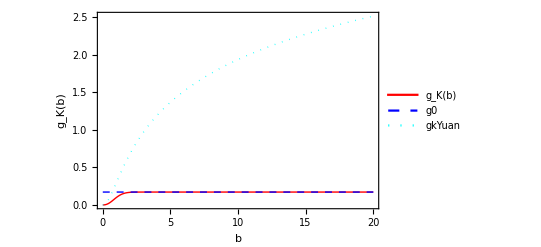

```mathematica
Plot[{gK[b],g0,gKYuan[b]},{b,0.01,20},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Cyan,Dotted}}, FrameLabel->{"b","g_K(b)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"g_K(b)", "g0","gkYuan" },{0.7,0.7}]]
```

K̃ from Collins, Rogers PRD 91,(2015)
 
 K̃ from Eq. (64) Collins, Rogers PRD 91,(2015)

```mathematica
Ktilde[b_,Q0_]:= KtildePert[bstar[b],mub[b]]-CF/(π beta0)Log[Log[Q0/Λ]/Log[mub[b]/Λ]]- gK[b];
```

```mathematica
KtildeYuan[b_,Q0_]:= KtildePert[bstar[b],mub[b]]-CF/(π beta0)Log[Log[Q0/Λ]/Log[mub[b]/Λ]]- gKYuan[b];
```

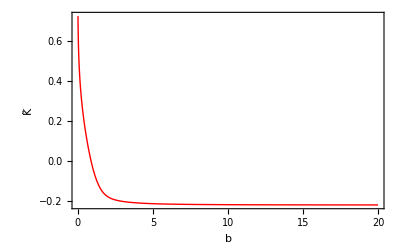

```mathematica
Plot[{Ktilde[b,Q0]},{b,0.01,20},PlotRange->{{0,20},{1,-0.5}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b","K̃"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

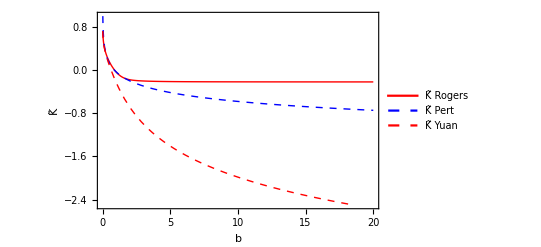

```mathematica
Plot[{Ktilde[b,Q0],KtildePert[b,Q0],KtildeYuan[b,Q0]},{b,0.01,20},PlotRange->{{0,20},{1,-2.5}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b","K̃"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"K̃ Rogers", "K̃ Pert","K̃ Yuan" },{0.7,0.7}]]
```

## Solution optimized for perturbative calculations (aka original CSS)

```mathematica
gKCSS[b_] := (as[mub[b]] CF)/π Log[1+b^2/bmax^2]; (*model for non perturbative dynamics in CS kernel from PRD 91*)
```

We observe typical narrowing of the distribution in b as Q grows

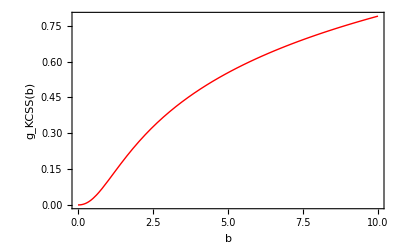

```mathematica
Plot[{gKCSS[b]},{b,0.01,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b","g_KCSS(b)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

## TMDs :

```mathematica
TMD0[kT_,Q_]:=TMD[0,Q]Exp[-kT^2/0.25] (* the canonical 0.25 width from Anselmino at 2.4 GeV2 *)
```

```mathematica
TMD25[kT_,Q_]:=TMD[0,Q]Exp[-kT^2/0.75] (* Peter's broadening at 25 GeV2*)
```

```mathematica
TMD[kT_,Q_] := NIntegrate[b BesselJ[0,kT b] Exp[-(b^2 0.25)/4]Exp[(Ktilde[b,Q0] Log[Q^2/Q0^2])/2],{b,0,100}] (* CSS solution for fixed Q0 valid at any scale above Q0 with Ktilde Rogers*)
```

```mathematica
TMDYuan[kT_,Q_] := NIntegrate[b BesselJ[0,kT b] Exp[-(b^2 0.25)/4]Exp[(KtildeYuan[b,Q0] Log[Q^2/Q0^2])/2],{b,0,100}] (* CSS solution for fixed Q0 valid at any scale above Q0 with Ktilde Yuan*)
```

```mathematica
TMDCSS[kT_,Q_] := NIntegrate[b BesselJ[0,kT b] Exp[-(b^2 0.25)/4]Exp[(-gKCSS[b] Log[Q^2/Q0^2])/2],{b,0,100}] (* CSS solution for OPE and b* valid at any scale above Q0*)
```

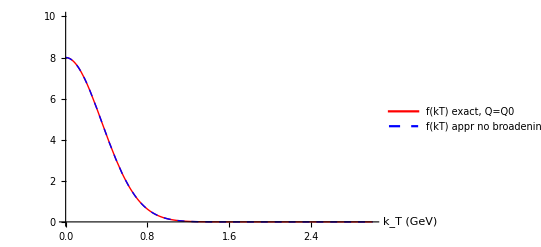

```mathematica
Plot[{TMD0[kT,Q0],TMD0[kT,Q0]},{kT,0,3},AxesLabel->{"k_T (GeV)"},PlotRange->{0,10},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}},PlotLegends->Placed[{"f(kT) exact, Q=Q0", "f(kT) appr no broadening"},{0.7,0.7}]]
```

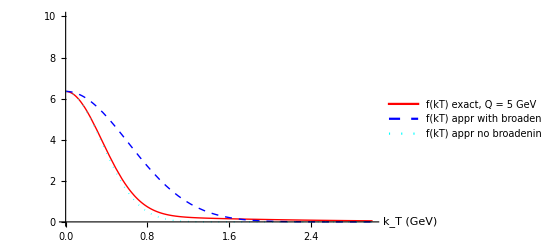

```mathematica
Plot[{TMD[kT,5.],TMD25[kT,5.],TMD0[kT,5.]},{kT,0,3},AxesLabel->{"k_T (GeV)"},PlotRange->{0,10},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Cyan,Dotted},{Thick,Blue,Dashed}},PlotLegends->Placed[{"f(kT) exact, Q = 5 GeV", "f(kT) appr with broadening", "f(kT) appr no broadening"},{0.7,0.7}]]
```

```mathematica
Coeff = TMD[0,5.]/TMDCSS[0,5.]
```

1.32583

```mathematica
CoeffYuan = TMD[0,5.]/TMDYuan[0,5.]
```

2.57202

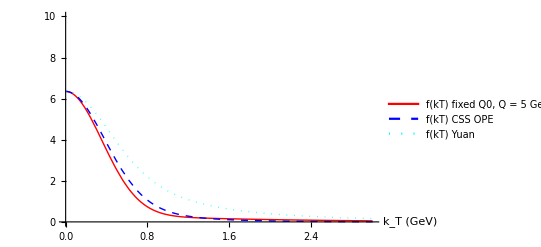

```mathematica
Plot[{TMD[kT,5.],Coeff TMDCSS[kT,5.], CoeffYuan TMDYuan[kT,5.]},{kT,0,3},AxesLabel->{"k_T (GeV)"},PlotRange->{0,10},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Cyan,Dotted},{Thick,Blue,Dashed}},PlotLegends->Placed[{"f(kT) fixed Q0, Q = 5 GeV", "f(kT) CSS OPE", "f(kT) Yuan"},{0.7,0.7}]]
```

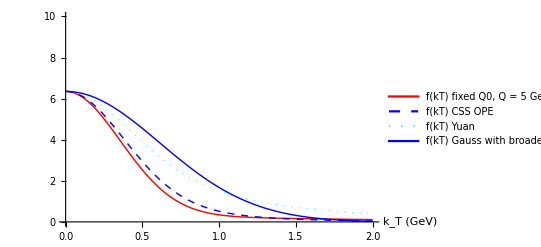

```mathematica
Plot[{TMD[kT,5.],Coeff TMDCSS[kT,5.], CoeffYuan TMDYuan[kT,5.],TMD25[kT,5.]},{kT,0,2},AxesLabel->{"k_T (GeV)"},PlotRange->{0,10},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Cyan,Dotted},{Thick,Blue}},PlotLegends->Placed[{"f(kT) fixed Q0, Q = 5 GeV", "f(kT) CSS OPE", "f(kT) Yuan", "f(kT) Gauss with broadening"},{0.7,0.7}]]
```

```mathematica
AverageKTCSS[Q_] := NIntegrate[kT^2 kT TMDCSS[kT,Q],{kT,0,10}]/NIntegrate[kT TMDCSS[kT,Q],{kT,0,10}]

AverageKT[Q_] := NIntegrate[kT^2 kT TMD[kT,Q],{kT,0,10}]/NIntegrate[kT TMD[kT,Q],{kT,0,10}]

AverageKT0[Q_] := NIntegrate[kT^2 kT TMD0[kT,Q],{kT,0,1000}]/NIntegrate[kT TMD0[kT,Q],{kT,0,1000}]
```

```mathematica
NIntegrate[kT^2 2 π kT/(π 0.25) Exp[-kT^2/0.25],{kT,0,1000}]
```

0.25

```mathematica
AverageKT0[Q0]
```

0.25

```mathematica
AverageKT[Q0]
```

NIntegrate::inumr: The integrand 1. b ⅇ^(-0.0625 b^2) BesselJ[0,b kT] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.25

```mathematica
AverageKT[5.]
```

NIntegrate::inumr: The integrand b ⅇ^(-0.0625 b^2+1.34707 (-0.171729 (1+Times[«2»])+(9.86865×10^-17)/Log[«1»]-16/27 Log[Times[«2»]])) BesselJ[0,b kT] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

10.7116

```mathematica
AverageKTCSS[5.]
```

NIntegrate::inumr: The integrand b (1+1. b^2)^(-0.798266/Log[(31.5237 (1+«1»))/b^2]) ⅇ^(-0.0625 b^2) BesselJ[0,b kT] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.780713